# Little Tests, One pyramidal lvl

## Start

```mathematica
(* Add to path packages *)
packageDirectory=FileNameJoin[{ParentDirectory[ParentDirectory[NotebookDirectory[]]],"1DPackage","*"}]
$Path=Join[$Path,FileNames[packageDirectory]];
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\1DPackage\*

```mathematica
<<"ReadSintel`"
<<"pyramid1d`"
<<"pyramidalStereoAll`"

methods={"","OverConstrained","SemiConstrained","Constrained","ConstrainedNewMethod"};
Do[
Get["pyramidalCyclope1D"<>met<>"`"]
,{met,methods}]
```

```mathematica
(* Declare path for SINTEL Data depending on user*)

baseSINTEL=Switch[$UserName,
"fieri","D:\\MastersMathematica\\Data\\Sintel",
"roys","/home/roys/datasets/SINTEL-stereo"
];
```

## Data

```mathematica
(* downscaling *)
r=2;
{ia,ib,id,io}=read[baseSINTEL,"Bamboo_1","0001",r,"final"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Image sections

```mathematica
(*{1,44},{1,102} arbitrary size to make the method faster *)
listDims={{100,100},{150,300},{200,200},{500,300},{500,200}}
ims=Table[
nx=dims[[1]]/r;
ny=dims[[2]]/r;


{iaa,ibb,idd,ioo}=ImageTake[#,{ny,ny+44},{nx,nx+102}]&/@{ia,ib,id,io};
Print[MinMax[Flatten[ImageData[idd]]]];
{iaa,ibb,idd}
,{dims,listDims}]

max=MinMax[Flatten[ImageData[id]]][[2]];
Print["max dv=", max]
```

{{100,100},{150,300},{200,200},{500,300},{500,200}}

{2.17754,38.6009}

{4.70419,12.5952}

{5.09229,7.39881}

{1.91684,28.6525}

{3.36446,26.8223}

{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

max dv=38.6009

## V0 function

```mathematica
removeClosest[s_]:=Block[{n,c},(n=Nearest[s];
c=SortBy[Table[{i,Norm[s[[i]]-n[s[[i]],2][[2]]]},{i,1,Length[s]}],(#[[2]])&][[1,1]];
Delete[s,c])];
removeClosest[s_]:=s/;Length[s]<2;
```

## Little functions

```mathematica
(*[steps,n,u,listv0,condition,e,{levels},ims]*)
bigTest[steps_,n_,u_,listv0_,condition_,e_,minmaxList_,imslist_]:=Block[{ic,depth, resTable,realPVTable,okTable,realOkPVTable,pos,pv,g0,nonresTable,nonrealPVTable},(
Table[
Table[
depth=stereoDepth[n,u,listv0,condition,im[[1]],im[[2]],minmax[[2]],minmax,Range[1,103,steps],Range[1,45],e,"ConstrainedNewMethod"];

(* We only keep converged solutions *)
resTable=Table[
Select[depth[[r]],#[[2]]=="converged"&]
(*depth[[r]]*)
,{r,45}];

(* We give right coordinates to each solution *)
realPVTable=Table[
pos=resTable[[r,All,5]]-resTable[[r,All,3]];
pv=Thread[{pos,resTable[[r,All,1]]}]
,{r,45}];

(* We only keep ok solutions *)
okTable=Table[
Select[depth[[r]],#[[2]]=="ok"&]
(*depth[[r]]*)
,{r,45}];

(* We give right coordinates to each solution *)
realOkPVTable=Table[
pos=okTable[[r,All,5]]-okTable[[r,All,3]];
pv=Thread[{pos,okTable[[r,All,1]]}]
,{r,45}];

(* We only keep NON converged solutions *)
nonresTable=Table[
Select[depth[[r]],(#[[2]]!="converged"&&#[[2]]!="ok")&]
(*depth[[r]]*)
,{r,45}];

(* We give right coordinates to each solution *)
nonrealPVTable=Table[
pos=nonresTable[[r,All,5]]-nonresTable[[r,All,3]];
pv=Thread[{pos,nonresTable[[r,All,1]]}]
,{r,45}];

(* We create g0 *)
g0=Graphics[{PointSize[0.009],Table[affiche[#,45-y]&/@realPVTable[[y]],{y,1,45}]}];
g0=Rasterize[Show[im[[1]],g0],ImageSize->ImageDimensions[im[[1]]]*5,ImageResolution->300];

{realPVTable,realOkPVTable,nonrealPVTable,g0}

,{minmax,minmaxList}]
,{im, imslist}]
)]
```

## Big Tests

### Test Design

For a synthetical displacement of 0.5:
 
•	Initial values range: {{0,1},{-1,1},{-1,0},{-2,2}}
•	Selection criteria:
	•	We filter direction (positive solutions only)
	•	Range {0, 1} 
	•	No errors allowed
•	Magnitude threshold for gradient is e=0.0001

(* Criterias to select a solution *)

newValCon=Select[tableNewVals,(#[[3]]==”converged”&& #[[1]]*#[[2]]>0 && 0<#[[2]]+#[[1]]<1)&,1];
newValAny=Select[tableNewVals,((#[[3]]≠ “ok”||#[[3]]≠ “oksign”||#[[3]]≠ “okmag”||#[[3]]≠ “converged”)&&#[[1]]*#[[2]]>0 && 0<#[[2]]+#[[1]]<1)&,1];
newValOk=Select[tableNewVals,((#[[3]]==”ok”||#[[3]]==”oksign”||#[[3]]==”okmag”)&& #[[1]]*#[[2]]>0 && 0<#[[2]]+#[[1]]<1)&,1];
noFakeConverge=Select[tableNewVals,(#[[3]]≠ “ok”||#[[3]]≠ “oksign”||#[[3]]≠ “okmag”||#[[3]]≠ “converged”)&,1];

### Test Run

```mathematica
Print["minmax dv=",MinMax[Flatten[ImageData[id]]]]
```

minmax dv={0.136895,38.6009}

```mathematica
(* Test values *)
testLevels={{1,1}};
e=0.0001;
n=0;
u=0;
steps=1;
```

```mathematica
(* Creating list of initial Values *)
range={-5,0};
listv0=Select[RandomReal[range,{1000,2}],(Sign[#[[1]]*#[[2]]]≥0 &&Abs[#[[1]]+#[[2]]]≤ Max[Abs[range]])&];
listv0=Nest[removeClosest,listv0,Length[listv0]-80];
ListPlot[listv0];
```

```mathematica
(* Creating condition *)
topbot={-50,0};
Clear[condition];
condition[x_]:=x[[1]]*x[[2]]>0 && topbot[[1]]<Total[x[[1;;2]]]<topbot[[2]];
```

```mathematica
(* Selection criteria values *)
scale=topbot;
affiche[{p_,v_},y_]:={RainbowColor[Rescale[v,scale,{0,1}]],Point[{p-0.5,y+0.5}]};
RainbowColor[z_]:=Blend[{Purple,Blue,Cyan,Green,Yellow,Orange,Red},z];
legendBar=BarLegend[{RainbowColor,{0,1}},Ticks->Table[{i,Rescale[i,{0,1},scale]},{i,Range[0,1,0.2]}]];
```

```mathematica
levelTable=Table[

bigTest[steps,n,u,listv0,condition,e,{levels},ims]

,{levels,testLevels}];
```

```mathematica
Print["levelTable Dimensions=",Dimensions[levelTable]]
```

levelTable Dimensions={1,5,1,4}

### More numbers

```mathematica
fontsize=16;
```

```mathematica
numbersTable=Table[

solution=ImageData[-ims[[which,3]]];
levelTable[[1,which,1,1]];

density=(Length[Flatten[DeleteDuplicates[#]&/@Floor[levelTable[[1,which,1,1,All,All,1]]]]])/(103.*45.);

vals=Table[
ps=Select[levelTable[[1,which,1,1,y,All,All]],1<Round[#[[1]]]<103&];
(ps[[All,2]]-solution[[y,Round[ps[[All,1]]]]])^2

,{y,Length[levelTable[[1,which,1,1]]]}];

rmse=Sqrt[Mean[Flatten[vals]]];

{Style["RMSE= ",FontSize->fontsize,FontFamily->"Times",Italic],rmse,Style["Density= ",FontSize->fontsize,FontFamily->"Times",Italic],density}

,{which,Length[ims]}]
```

{{RMSE= ,9.13158,Density= ,0.360518},{RMSE= ,2.05523,Density= ,0.438188},{RMSE= ,1.42366,Density= ,0.472708},{RMSE= ,8.32512,Density= ,0.352319},{RMSE= ,3.31658,Density= ,0.415534}}

### Images

```mathematica
Style["Rmse= ",FontSize->fontsize,FontFamily->"Times",Italic]
```

Rmse=

```mathematica
imagesTable=Table[

solution=Image[Table[Map[RainbowColor,imd],{imd,ImageData[Rescale[-ims[[which,3]],scale,{0,1}]]}]];

images=ConformImages[Rasterize[Image[#],ImageResolution->500]&/@Flatten[{ims[[which,1;;2]],levelTable[[1,which,1,4]],solution}],{4000}];

Grid[{images,numbersTable[[which]]}]

,{which,Length[ims]}];
```

```mathematica
imFinal=Legended[Grid[Flatten[{imagesTable},{{2},{1}}]],legendBar]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
RMSE=  | 9.13158 | Density=  | 0.360518
-Graphics- | -Graphics- | -Graphics- | -Graphics-
RMSE=  | 2.05523 | Density=  | 0.438188
-Graphics- | -Graphics- | -Graphics- | -Graphics-
RMSE=  | 1.42366 | Density=  | 0.472708
-Graphics- | -Graphics- | -Graphics- | -Graphics-
RMSE=  | 8.32512 | Density=  | 0.352319
-Graphics- | -Graphics- | -Graphics- | -Graphics-
RMSE=  | 3.31658 | Density=  | 0.415534

```mathematica
nbname=StringDelete[Last@FileNameSplit@NotebookFileName[],".nb"];
```

```mathematica
figsDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"figs"}];

Export[FileNameJoin[{figsDirectory,nbname<>"-im.pdf"}],imFinal]
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\Figures\figs\sintel-bamboo-final-im.pdf

### More in depth

```mathematica
lvl=5;
```

```mathematica
k=2;
{ka,kb}=ImageData[#][[k]]&/@ims[[4,1;;2]];
pyra=pyrFuncGen[ka,lvl];
pyrb=pyrFuncGen[kb,lvl];
pyrab=Flatten[{pyra, pyrb},{{2},{1},{3}}];
```

```mathematica
lineTest[n,u,listv0,condition,Range[1,130],pyrab[[1;;1]],e,"ConstrainedNewMethod"]
```

{{0.,0.,sign,1},{0.,0.,sign,2},{0.,0.,sign,3},{0.,0.,sign,4},{-2.08429,-4.48525,converged,5},{-3.28962,-2.15327,converged,6},{-0.593337,-5.56582,converged,7},{-4.92224,-0.600994,converged,8},{-4.1512,-1.30283,converged,9},{-4.10268,-1.35841,converged,10},{-3.77576,-1.68177,converged,11},{-2.98052,-2.48068,converged,12},{-2.4639,-2.97498,converged,13},{-1.59999,-3.83033,converged,14},{-5.51845,-0.246431,converged,15},{-4.70878,-1.03973,converged,16},{-3.6189,-2.14038,converged,17},{-2.49932,-3.26642,converged,18},{-1.47758,-4.28965,converged,19},{-0.593768,-5.16607,converged,20},{0.,0.,sign,21},{-1.84805,-1.49392,converged,22},{-4.09545,-1.74116,converged,23},{-4.26217,-1.57428,converged,24},{-3.67417,-2.16852,converged,25},{-2.75725,-3.08637,converged,26},{-2.09011,-3.76028,converged,27},{-1.45591,-4.39323,converged,28},{-0.898932,-4.9548,converged,29},{-0.536058,-5.34562,converged,30},{-5.71802,-0.153474,converged,31},{-5.23691,-0.711283,converged,32},{-4.10241,-1.82549,converged,33},{-5.00677,-2.14261,converged,34},{-4.45544,-1.25585,converged,35},{-3.15123,-2.5236,converged,36},{-0.902231,-3.64955,converged,37},{-1.20714,-4.47885,converged,38},{-10.8825,-0.311145,converged,39},{0.,0.,sign,40},{-6.7907,-3.23793,converged,41},{0.,0.,sign,42},{0.,0.,sign,43},{-3.88271,-22.7524,converged,44},{-4.13582,-6.92573,converged,45},{-3.5487,-7.59983,converged,46},{-2.71263,-14.4739,converged,47},{-1.86277,-9.32735,converged,48},{-0.991849,-10.2225,converged,49},{0.,0.,sign,50},{-0.41993,-3.52346,ok,51},{-0.131326,-0.0949838,converged,52},{-1.14444,-0.428169,converged,53},{0.,0.,sign,54},{0.,0.,sign,55},{0.,0.,sign,56},{0.,0.,sign,57},{-6.80749,-5.81126,converged,58},{-6.59661,-6.10709,converged,59},{-11.1837,-1.92709,converged,60},{-10.0755,-3.02262,converged,61},{-9.57248,-3.55908,converged,62},{-9.22027,-3.96746,converged,63},{-8.79467,-4.41298,converged,64},{-8.61277,-4.39709,converged,65},{-7.61001,-5.39535,converged,66},{-4.17441,-8.93025,converged,67},{-16.164,-0.440659,ok,68},{0.,0.,sign,69},{0.,0.,sign,70},{0.,0.,sign,71},{0.,0.,sign,72},{0.,0.,sign,73},{0.,0.,sign,74},{-0.796336,-1.6373,ok,75},{-4.75903,-2.45435,converged,76},{-2.4087,-1.41425,ok,77},{-2.88892,-4.01281,converged,78},{-1.90657,-4.96923,converged,79},{-0.747629,-6.43473,ok,80},{-0.578556,-4.79703,converged,81},{-0.932686,-1.65168,converged,82},{-5.71145,-0.497979,converged,83},{-4.40276,-1.61755,converged,84},{-0.71602,-3.27427,converged,85},{-0.601169,-4.05789,converged,86},{-7.21726,-0.0578507,converged,87},{-6.67277,-0.765656,converged,88},{-5.13113,-2.11597,converged,89},{-3.46875,-5.3323,converged,90},{-2.20256,-6.391,converged,91},{-1.61643,-7.29768,converged,92},{-1.38173,-5.93083,converged,93},{-0.365908,-9.11724,converged,94},{0.,0.,sign,95},{-1.19868,-2.13027,converged,96},{-0.249202,-3.11346,converged,97},{-4.13454,-0.280786,converged,98},{-3.67347,-0.748897,converged,99},{-2.03995,-2.34557,converged,100},{-1.68137,-2.08058,ok,101},{0.,0.,sign,102},{0.,0.,sign,103},{0.,0.,sign,104},{0.,0.,sign,105},{0.,0.,sign,106},{0.,0.,sign,107},{0.,0.,sign,108},{0.,0.,sign,109},{0.,0.,sign,110},{0.,0.,sign,111},{0.,0.,sign,112},{0.,0.,sign,113},{0.,0.,sign,114},{0.,0.,sign,115},{0.,0.,sign,116},{0.,0.,sign,117},{0.,0.,sign,118},{0.,0.,sign,119},{0.,0.,sign,120},{0.,0.,sign,121},{0.,0.,sign,122},{0.,0.,sign,123},{0.,0.,sign,124},{0.,0.,sign,125},{0.,0.,sign,126},{0.,0.,sign,127},{0.,0.,sign,128},{0.,0.,sign,129},{0.,0.,sign,130}}

```mathematica
(* Creating list of initial Values *)
range={-3,0};
listv0=Select[RandomReal[range,{1000,2}],(Sign[#[[1]]*#[[2]]]≥0 &&Abs[#[[1]]+#[[2]]]≤ Max[Abs[range]])&];
listv0=Nest[removeClosest,listv0,Length[listv0]-80];
ListPlot[listv0];
```

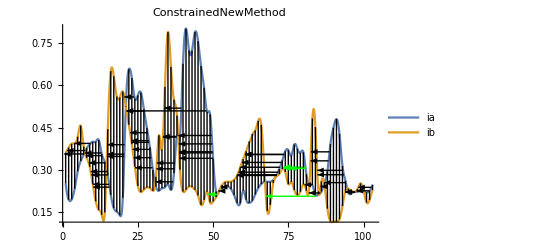

```mathematica
seeAllLine[n,u,listv0,condition,Range[1,103],pyrab[[1;;1]],e,"ConstrainedNewMethod"]
```